# Project report

## Flow calibration comparison

D Malan

Department of Chemistry
University of Pretoria

04 January 2020

## Introduction

The flow in the GC depends on the head pressure. It is difficult to measure the average linear flow rate, because the short column and high flow does not allow the traditional manual  measurement of the elution time of an unretained compound. If the pressure gauge changed and indicates a different pressure from the previous gauge, the flow will be different.

## Experimental

I measured the flow on 17 December 2019, and again on 3 February 2020, after installation of a new gauge.

The column lengths were not identical. The column used in December was probably shorter than the column used in February.

## Calculations

The data for the previous gauge:

```mathematica
olddata= Import["C:\\Users\\fskdm\\My PhD\\Projects\\2019_12_20_PhD_Last_Project\\2019_12_17_Flow_measurement.xlsx"];
```

```mathematica
TableForm[olddata]
```

Head pressure (psi)
Volume (ml)
Time (s)
Time (min)
Flow (ml/min) | 8.
2.
11.2
0.186667
10.7143 | 8.
2.
11.11
0.185167
10.8011 | 8.
1.5
8.31
0.1385
10.8303 | 8.
2.
10.99
0.183167
10.919 | 12.
2.
3.58
0.0596667
33.5196 | 12.
2.
3.63
0.0605
33.0579 | 12.
2.
3.61
0.0601667
33.241 | 12.
2.
3.7
0.0616667
32.4324 | 12.
2.
3.75
0.0625
32. | 16.
2.
2.13
0.0355
56.338 | 16.
10.
9.91
0.165167
60.5449 | 16.
10.
11.88
0.198
50.5051 | 16.
2.
2.07
0.0345
57.971 | 16.
2.
1.99
0.0331667
60.3015 | 20.
8.
5.31
0.0885
90.3955 | 20.
8.
5.38
0.0896667
89.2193 | 20.
8.
5.33
0.0888333
90.0563 | 20.
8.
5.32
0.0886667
90.2256 | 20.
10.
6.73
0.112167
89.153 | 7.
1.
8.79
0.1465
6.82594 | 7.
1.
8.55
0.1425
7.01754 | 7.
1.
8.46
0.141
7.0922 | 7.
1.
8.46
0.141
7.0922 | 7.
1.
8.35
0.139167
7.18563
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
oldline = Fit[olddata[[1]][[2;;,{1,5}]], {1,x},x]
```

-39.7755+6.29333 x

```mathematica
plotolddata = olddata[[1]][[2;;,{1,5}]]
```

{{8.,10.7143},{8.,10.8011},{8.,10.8303},{8.,10.919},{12.,33.5196},{12.,33.0579},{12.,33.241},{12.,32.4324},{12.,32.},{16.,56.338},{16.,60.5449},{16.,50.5051},{16.,57.971},{16.,60.3015},{20.,90.3955},{20.,89.2193},{20.,90.0563},{20.,90.2256},{20.,89.153},{7.,6.82594},{7.,7.01754},{7.,7.0922},{7.,7.0922},{7.,7.18563}}

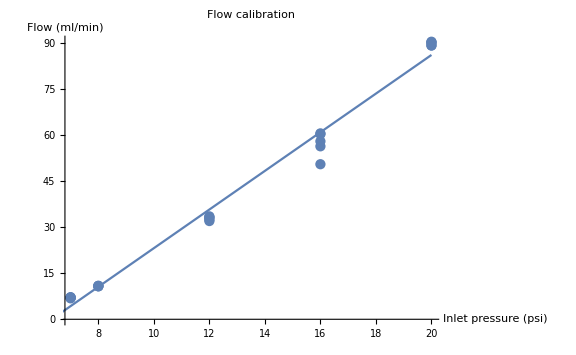

```mathematica
Show[
	ListPlot[plotolddata
, PlotLabel-> "Flow calibration"
,AxesLabel->{"Inlet pressure (psi)","Flow (ml/min)"} 
, ImageSize->Large]
	, Plot[line, {x, 0, 20}]
]
```

Data for the new gauge:

```mathematica
newdata =Import["C:\\Users\\fskdm\\My PhD\\Projects\\2020_02_03_Gauge_Install\\2020_02_03_Column_Flow.xlsx"];
```

```mathematica
TableForm[newdata[[1]]]
```

Mon 3 Feb 2020 15:30:00GMT+2. | Column flow |  |  |  | 
 | Room temperature: 22°C |  |  |  | 
 | Pressure: | 1.4 | kg/cm^2 |  | 
 | Volume of gas | Time | Time | Flow | 
 | ml | s | min | ml/min | 
 | 8. | 7.5 | 0.125 | 64. | 
 | 10. | 9.7 | 0.161667 | 61.8557 | 
 | 10. | 9.74 | 0.162333 | 61.6016 | 
 |  |  |  | 62.4858 | Average
 |  |  |  |  | 
 | Pressure: | 1.2 | kg/cm^2 |  | 
 | Volume of gas | Time | Time | Flow | 
 | ml | s | min | ml/min | 
 | 10. | 11.6 | 0.193333 | 51.7241 | 
 | 10. | 12.02 | 0.200333 | 49.9168 | 
 | 10. | 11.55 | 0.1925 | 51.9481 | 
 |  |  |  | 51.1963 | Average
 |  |  |  |  | 
 | Pressure: | 1. | kg/cm^2 |  | 
 | Volume of gas | Time | Time | Flow | 
 | ml | s | min | ml/min | 
 | 10. | 15.06 | 0.251 | 39.8406 | 
 | 10. | 15.17 | 0.252833 | 39.5517 | 
 | 10. | 15.19 | 0.253167 | 39.4997 | 
 |  |  |  | 39.6307 | 
 |  |  |  |  | 
 | Pressure: | 0.8 | kg/cm^2 |  | 
 | Volume of gas | Time | Time | Flow | 
 | ml | s | min | ml/min | 
 | 10. | 20.58 | 0.343 | 29.1545 | 
 | 2. | 4.09 | 0.0681667 | 29.3399 | 
 | 8. | 16.24 | 0.270667 | 29.5567 | 
 |  |  |  | 29.3503 | 
 |  |  |  |  | 
 | Pressure: | 0.6 | kg/cm^2 |  | 
 | Volume of gas | Time | Time | Flow | 
 | ml | s | min | ml/min | 
 | 2. | 5.79 | 0.0965 | 20.7254 | 
 | 2. | 5.79 | 0.0965 | 20.7254 | 
 | 2. | 5.7 | 0.095 | 21.0526 | 
 |  |  |  | 20.8345 | 
 |  |  |  |  | 
 | Pressure: | 0.4 | kg/cm^2 |  | 
 | Volume of gas | Time | Time | Flow | 
 | ml | s | min | ml/min | 
 | 2. | 9.65 | 0.160833 | 12.4352 | 
 | 2. | 9.66 | 0.161 | 12.4224 | 
 | 2. | 9.64 | 0.160667 | 12.4481 | 
 |  |  |  | 12.4352 |

```mathematica
averagelines = 1+Range[6]*8
```

{9,17,25,33,41,49}

```mathematica
newflows = newdata[[1,averagelines,5]]
```

{62.4858,51.1963,39.6307,29.3503,20.8345,12.4352}

```mathematica
pressurelines = 3+(Range[6]-1)*8
```

{3,11,19,27,35,43}

```mathematica
newpressures =newdata[[1, pressurelines,3]]/0.070307
```

{19.9127,17.068,14.2233,11.3787,8.534,5.68933}

```mathematica
plotnewdata = Partition[Riffle[newpressures, newflows],2]
```

{{19.9127,62.4858},{17.068,51.1963},{14.2233,39.6307},{11.3787,29.3503},{8.534,20.8345},{5.68933,12.4352}}

```mathematica
newline= Fit[plotnewdata, {1,x},x]
```

-9.2193+3.53161 x

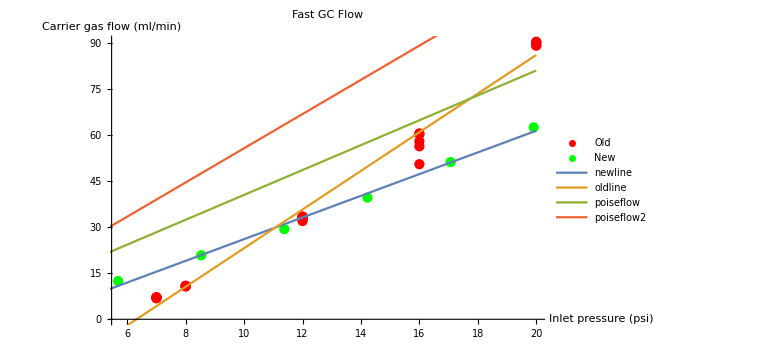

```mathematica
Show[
ListPlot[{plotolddata, plotnewdata}
, PlotLabel->"Fast GC Flow"
, AxesLabel->{"Inlet pressure\n(psi)","Carrier gas flow\n(ml/min)"}
, PlotStyle->{Red, Green}
, ImageSize->Large
,PlotLegends->{"Old","New"}
]
,Plot[{newline, oldline, poiseflow,poiseflow2},{x,5,20}, PlotLegends->"Expressions"]
]
```

```mathematica
TableForm[{newline, oldline}]
```

-9.2193+3.53161 x
-39.7755+6.29333 x

### Theoretical calculation

WolframAlphaQueryResults

WolframAlphaQueryResults

```mathematica
poiseflow = UnitConvert[(Pi*Quantity[0.25/2, "Millimeters"]^4*UnitConvert[Quantity[x, "psi"]- Quantity[0, "Hectopascals"], "Pascals"])/(8*Quantity[8.9*10^-6, "Pascals"*"Seconds"]*Quantity[1.1, "Meters"]), "Milliliters"/"Minutes"]
```

4.05124 x mL/min

```mathematica
poiseflow2 = UnitConvert[(Pi*Quantity[0.25/2, "Millimeters"]^4*UnitConvert[Quantity[x, "psi"], "Pascals"])/(8*Quantity[8.9*10^-6, "Pascals"*"Seconds"]*Quantity[0.8, "Meters"]), "Milliliters"/"Minutes"]
```

5.57045 x mL/min

## Discussion

The two gauges do not show exactly the same flows at the same indicated pressures, but the theoretical calculations suggest that the difference in flows can be attributed to difference in the length of the columns.

## Conclusion

The gauges are precise enough for repeatable flow settings, but for accurate flow measurement, set the FID flame hydrogen to zero and measure carrier gas flow at the detector.

## Recommendations

When setting the gas flows, use the flow through the detector as an indication.